```mathematica
SetDirectory[NotebookDirectory[]];
```

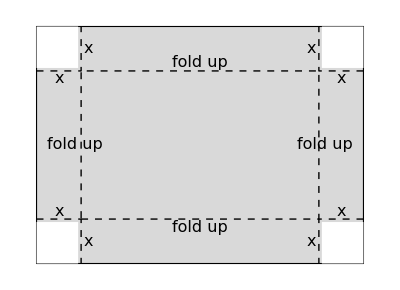

```mathematica
x=1.5;
Show[
Graphics[{LightGray,EdgeForm[Black],Rectangle[{0,0},{11,8}]}],

Graphics[{White,EdgeForm[None],Rectangle[{0,0},{x-0.1,x-0.1}]}],
Graphics[{White,EdgeForm[None],Rectangle[{0,8-x+0.1},{x-0.1,8}]}],
Graphics[{White,EdgeForm[None],Rectangle[{11-x+0.1,8-x+0.1},{11,8}]}],
Graphics[{White,EdgeForm[None],Rectangle[{11-x+0.1,0},{11,x-0.1}]}],

Graphics[{Dashed,Line[{{x,x},{11-x,x},{11-x,8-x},{x,8-x},{x,x}}]}],

Graphics[{Dashed,Line[{{0,x},{x,x},{x,0}}]}],
Graphics[{Dashed,Line[{{0+11,x},{-x+11,x},{-x+11,0}}]}],
Graphics[{Dashed,Line[{{0,-x+8},{x,-x+8},{x,8}}]}],
Graphics[{Dashed,Line[{{11,-x+8},{-x+11,-x+8},{-x+11,8}}]}],

Epilog->{
Text[Style[HoldForm[x],16],{x/2,x+0.25}],
Text[Style[HoldForm[x],16],{x+0.25,x/2}],
Text[Style[HoldForm[x],16],{11-x/2,x+0.25}],
Text[Style[HoldForm[x],16],{x+0.25,8-x/2}],
Text[Style[HoldForm[x],16],{11-x/2,8-x-0.25}],
Text[Style[HoldForm[x],16],{11-x-0.25,8-x/2}],
Text[Style[HoldForm[x],16],{x/2,8-x-0.25}],
Text[Style[HoldForm[x],16],{11-x-0.25,x/2}],
Rotate[Text[Style["fold up",16],{11/2,x-0.3}],Pi],
Text[Style["fold up",16],{11/2,8-x+0.3}],
Rotate[Text[Style["fold up",16],{x-0.2,8/2}],Pi/2],
Rotate[Text[Style["fold up",16],{11-x+0.2,8/2}],-Pi/2]
}
]
Export[{"box.svg","box.pdf"},%];
```